## General functional derivatives

Homogeneous case

```mathematica
M[xT_]:=xT^4-Abs[xT](1-2 xT^2);
```

Heterogeneous case

```mathematica
dτ[xT_,x_]:=1/2 x (-x+xT) If[x*xT>=0,1,0]*If[-Abs[x]+Abs[xT]>=0,1,0] *If[xT==0,0,Sign[xT]] (x+If[xT==0,0,Sign[xT]])+1/2 x xT*If[-x xT>0,1,0] (x+If[xT==0,0,Sign[xT]])^2;
```

## Polynomial distribution (Sixth order) --- Optimal delta peak resetting

```mathematica
pbc[a_,xT_]:= a xT^2+(4-3 a) xT^4+7/30 (-9+8 a) xT^6;
Manipulate[Plot[pbc[a,x],{x,-1,1},PlotRange->{{-1,1},{0,2}}],{a,0,1/23 (117+√8169)}]
```

Maximum value of a to ensure positivity

{{a→119021/13152}}

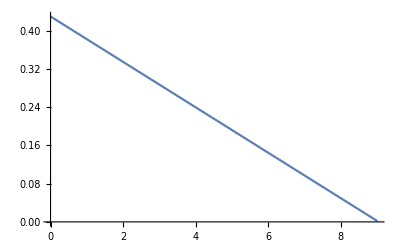

```mathematica
mbc[a_]:=Integrate[pbc[a,xT]*M[xT],{xT,0,1}]
Solve[mbc[a]==0,a]
Plot[mbc[b],{b,0,1/23 (117+√8169)}]
```

### No transition is found using homogeneous resetting. Perturbation around r=0 :

```mathematica
Integrate[2*(dτ[xT,x]+dτ[-xT,x])/2 pbc[a,xT],{xT,0,1},Assumptions->{x>0,a>0,a<1/23 (117+√8169),x<1}]
mubc[x_,a_]:=1/480 (171 x^2-12 a x^2-217 x^3+4 a x^3+20 a x^5+20 a x^6+32 x^7-24 a x^7+32 x^8-24 a x^8-9 x^9+8 a x^9-9 x^10+8 a x^10)
Manipulate[Plot[mubc[x,a],{x,0,1}],{a,0,1/23 (117+√8169)}]
```

1/480 (171 x^2-12 a x^2-217 x^3+4 a x^3+20 a x^5+20 a x^6+32 x^7-24 a x^7+32 x^8-24 a x^8-9 x^9+8 a x^9-9 x^10+8 a x^10)

```mathematica
Solve[D[1/480 (171 x^2-12 a x^2-217 x^3+4 a x^3+20 a x^5+20 a x^6+32 x^7-24 a x^7+32 x^8-24 a x^8-9 x^9+8 a x^9-9 x^10+8 a x^10),x]==0,x]
```

{{x→0},{x→1},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,1]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,2]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,3]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,4]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,5]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,6]},{x→Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,7]}}

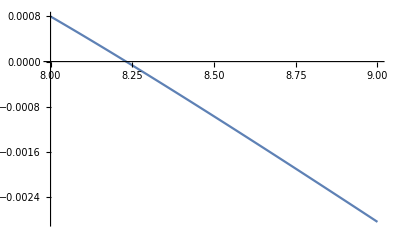

{{a→Root8.23Root[-13803117256351312793+51900773773396974584 #1-76841658253344281952 #1^2+56163075109201698816 #1^3-20806992065339584768 #1^4+3706395239263512576 #1^5-338224069179506688 #1^6+16360974380171264 #1^7-399969497382912 #1^8+3893966667776 #1^9&,1]8.23125087476942}}

```mathematica
Plot[mubc[Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,2],a],{a,8,9}]
Solve[mubc[Root[-342+24 a+(309+12 a) #1+(309+12 a) #1^2+(309-88 a) #1^3+(309-208 a) #1^4+(85-40 a) #1^5+(-171+152 a) #1^6+(-90+80 a) #1^7&,2],a]==0,a]
```

Transition at a=8.23125087476942. After that value, r=0 is not optimal

## Polynomial distribution P_(pol,n)(x_n)=a_n(b)+b|x|^n

### n=1

```mathematica
pb[x_,b_]:=(1-b)/2+b*Abs[x]
Manipulate[Plot[pb[x,b],{x,-1,1},PlotRange->{{-1,1},{0,2}}],{b,-1,1}]
```

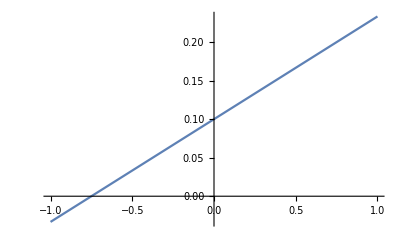

```mathematica
m2[b_]:=Integrate[pb[xT,b]*M[xT],{xT,0,1}]
Plot[m2[b],{b,-1,1}]
```

Homogeneous transition at b=-0.75

```mathematica
Integrate[2*(dτ[xT,x]+dτ[-xT,x])/2 pb[xT,b],{xT,0,1},Assumptions->{x>0,Abs[b]<=1,x<1}]
```

1/24 (3 x^2+3 b x^2-6 x^3-4 b x^3+3 x^4-b x^4+2 b x^5)

```mathematica
mu2[x_,b_]:=1/24 (3 x^2+3 b x^2-6 x^3-4 b x^3+3 x^4-b x^4+2 b x^5)
```

```mathematica
Manipulate[Plot[mu2[x,b],{x,0,1}],{b,-1,1}]
```

```mathematica
1/24 (3 x^2+3 b x^2-6 x^3-4 b x^3+3 x^4-b x^4+2 b x^5)/.x->1
D[1/24 (3 x^2+3 b x^2-6 x^3-4 b x^3+3 x^4-b x^4+2 b x^5),{x,1}]/.x->1
D[1/24 (3 x^2+3 b x^2-6 x^3-4 b x^3+3 x^4-b x^4+2 b x^5),{x,2}]/.x->1
```

0

0

1/24 (6+10 b)

Homogeneous transition at b=-0.6

### n=2

```mathematica
pb2[x_,b_]:=1/6 (3-2 b)+b*x^2
Manipulate[Plot[pb2[x,b],{x,-1,1},PlotRange->{{-1,1},{0,2}}],{b,-0.75,1.5}]
```

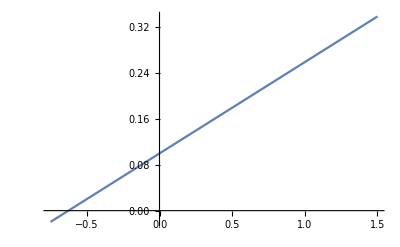

{{b→-42/67}}

```mathematica
m22[b_]:=Integrate[pb2[xT,b]*M[xT],{xT,0,1}]
Plot[m22[b],{b,-0.75,1.5}]
Solve[m22[b]==0,b]
```

Homogeneous transition at  b=-42/67

```mathematica
Integrate[2*(dτ[xT,x]+dτ[-xT,x])/2 pb2[xT,b],{xT,0,1},Assumptions->{x>0,Abs[b]<=1,x<1}]
```

1/24 (3 x^2+3 b x^2-6 x^3-3 b x^3+3 x^4-2 b x^4+b x^5+b x^6)

```mathematica
mu2[x_,b_]:=1/24 (3 x^2+3 b x^2-6 x^3-3 b x^3+3 x^4-2 b x^4+b x^5+b x^6)
```

```mathematica
Manipulate[Plot[mu2[x,b],{x,0,1}],{b,-0.75,1.5}]
```

```mathematica
1/24 (3 x^2+3 b x^2-6 x^3-3 b x^3+3 x^4-2 b x^4+b x^5+b x^6)/.x->1
D[1/24 (3 x^2+3 b x^2-6 x^3-3 b x^3+3 x^4-2 b x^4+b x^5+b x^6),{x,1}]/.x->1
D[1/24 (3 x^2+3 b x^2-6 x^3-3 b x^3+3 x^4-2 b x^4+b x^5+b x^6),{x,2}]/.x->1
```

0

0

1/24 (6+14 b)

```mathematica
Solve[1/24 (6+14 b)==0,b]
```

{{b→-3/7}}

Homogeneous transition at b=-3/7